```mathematica
rho[x_,z_]:=0.5(1+Erf[(z-z0)*yv+pert*Cos[x]])(ph-pl)+pl;
pl=1.0;ph=1.833;pert=0.5;z0=3.2;yv=4096/(1.5*32);
```

```mathematica
p[x_,z_]=∫(0.5(1+Erf[(z-z0)*yv+pert*Cos[x]])(ph-pl)+pl)ⅆz
```

-4.5328+0.00275373 2.71828^(-7281.78 (3.2-1. z-0.00585938 Cos[x])^2)+1.4165 z+0.0082998 Cos[x]+(1.3328-0.4165 z-0.00244043 Cos[x]) Erf[273.067-85.3333 z-0.5 Cos[x]]

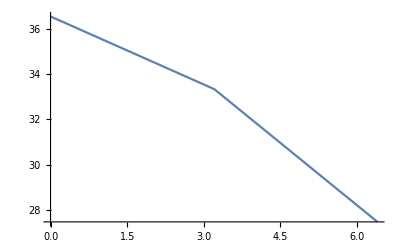

```mathematica
Plot[35-p[Pi,z]-1.671384954238853,{z,0,2*z0}]
```

```mathematica
35-p[Pi,3.2]-1.671384954238853
```

33.3335

```mathematica
35-p[Pi,0]-1.671384954238853
```

36.5345